1. naloga: Dan je pravilen šestkotnik s stranico r. Kolikšna je ploščina kolobarja, ki ga določata včrtana in očrtana krožnica?

2. naloga: Sin je 3 leta starejši od hčere, mati pa je 23 let starejša od sina. Pred 6 leti je imela mati 4 krat toliko let kot sin in hči skupaj. Koliko je star vsak od njih?

```mathematica
Solve[s==h+3&&m==s+23&&m-6==4*(s-6+h-6),{s,h,m}]
```

{{s→11,h→8,m→34}}

```mathematica
seznam={5,4,2};
seznam[[2]]
```

4

3. naloga: Koliko začetnih členov zaporedja s splošnim členom a_n = 16 - 2n moramo sešteti, da bo vsota enaka 36?

```mathematica
Solve[Sum[16-2n,{n, x}]==36, x] // First
```

{x→3}

4. naloga: Poišči vsa kompleksna števila, ki zadoščajo enačbi z̄ = z^2

```mathematica
Solve[Conjugate[z]==z^2,z]
```

{{z→0},{z→1},{z→-1/2-(ⅈ √3)/2},{z→-1/2+(ⅈ √3)/2}}

5. naloga: Dokaži, da je 1 rešitev enačbe a x - 2 b x + c = 0, če a, b in c sestavljajo aritmetično zaporedje.

```mathematica
Solve[a x^2 -2b x +c ==0/.{b->a+k,c->a+2k}, x]
```

{{x→1},{x→(a+2 k)/a}}

6. naloga: Izračunaj vrednost izraza (sin α + sin β)/(cos^2(α - β) - sin^2(β-α)) za kota α = 1830°  in  β = 270°.

```mathematica
(Sin [α]+Sin [β])/(Cos[(α-β)]^2-Sin[(β-α)]^2)/.{{α->1830Degree, β->270Degree},{α->14Degree,β->770Degree}}
```

{1,(Cos[40 °]+Sin[14 °])/(-5/8+(√5)/8+1/16 (1+√5)^2)}

7. naloga: Določi vrednost parametra a v enačbi (2a x+3a)/(3a + 5x)=(3a-4)/(3a + 5x), da bo  x = 2  rešitev enačbe.

8. naloga: Na kakšne načine lahko plačamo poštnino 2.27 EUR z znamkami za 10, 23 in 37 centov?

9. naloga: Poišči štirimestno število, ki je popoln kvadrat in katerega prvi dve števki sta med seboj enaki, drugi dve pa prav tako med seboj enaki.

```mathematica
(* stevilo aabb *)
Solve[{a*1100+b*11==m^2, 9≥ a>0, 9≥ b≥ 0, m>0},{a, b, m},Integers]
```

{{a→7,b→4,m→88}}

10. naloga: Na kocko s stranico a postavimo drugo kocko s telesno diagonalo, enako stranici prve kocke, na drugo kocko spet tretjo s telesno diagonalo, enako stranici druge kocke, in to ponavljamo brez konca. Izračunaj višino in prostornino tako dobljenega telesa.

```mathematica
a*Sum[1/(Sqrt[3]^i),{i,0,Infinity}] //FullSimplify
```

1/2 (3+√3) a

```mathematica
a^3+Sum[1/Sqrt[3]^(3i), {i,0,Infinity}] //FullSimplify
```

3/26 (9+√3)+a^3

11. naloga: Določi linearno funkcijo y = kx + n, ki ima pri x = -2 vrednost 3, pri x = 1 pa vrednost - 6, ter nariši njen graf tako, da bosta enoti na koordinatnih oseh enako veliki.

```mathematica
izraz=k*x+n
```

n+k x

```mathematica
prep=Solve[{izraz==3/. x->-2, izraz==-6/.x->1},{k,n}] //First
```

{k→-3,n→-3}

```mathematica
izraz/. prep
```

-3-3 x

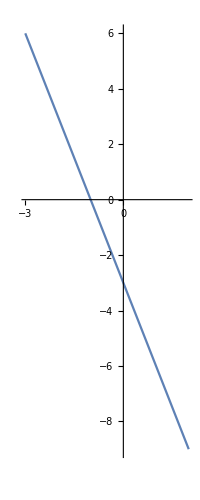

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[izraz/.prep]

```mathematica
Plot[izraz/.prep, {x,-3,2}, AspectRatio->Automatic]
```

12. naloga: Določi inverzno funkcijo funkcije f(x) = x^-1+ 2 ter nariši grafa obeh funkcij v istem koordinatnem sistemu.

```mathematica
f=x^-1 + 2
```

2+1/x

```mathematica
inverzPrep=Solve[y==f/.{x->y, y->x},y]//First
```

{y→1/(-2+x)}

```mathematica
inverz=y/.inverzPrep
```

1/(-2+x)

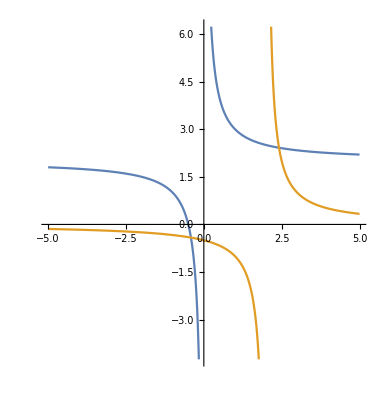

```mathematica
Plot[{f,inverz},{x,-5,5}, AspectRatio->Automatic]
```

```mathematica
(*komentar*)
```